```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]
```

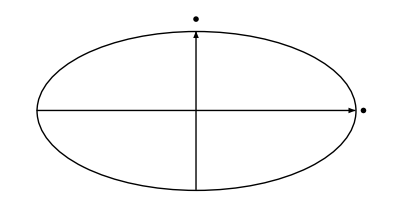

```mathematica
basicStatMechLecture4Fig4 = Graphics[{
Circle[{0,0}, {2, 1}],
Arrow[{{-2,0},{2,0}}],
Arrow[{{0, -1},{0, 1}}],
Text[MaTeX["p"], {0, 1.15}],
Text[MaTeX["x"], {2.1, 0}]
}]
```

```mathematica
peeters`exportForLatex["basicStatMechLecture4Fig4",basicStatMechLecture4Fig4]
```

{basicStatMechLecture4Fig4.eps,basicStatMechLecture4Fig4pn.png}